```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]={{ⅈ 0.0001-0+ω,-t,0,0,0,0,0},{-t,ⅈ 0.0001-0+ω,-t,0,0,0,0},{0,-t,ⅈ 0.0001-0+ω,-t,0,0,0},{0,0,-t,ⅈ 0.0001-0+ω,-t,0,0},{0,0,0,-t,ⅈ 0.0001-0+ω,-t,0},{0,0,0,0,-t,ⅈ 0.0001-0+ω,-t},{0,0,0,0,0,-t,ⅈ 0.0001-0+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],A:=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,6000];J=J]
```

```mathematica
Clear[LEFT]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,0.0001,1,0]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,0.0001,1,0].T2[1].LEFT[ω,0.0001,1,0].T2[1]].g[ω,0.0001,1,0]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,0.0001,1,0].T2[1].LEFT[ω,0.0001,1,0].T2[1]].g[ω,0.0001,1,0]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,0.0001,1,0].T1[1].SR[ω,0.0001,1,0].T1[1]].SL[ω,0.0001,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].SL[ω,0.0001,1,0].T1[1]].SR[ω,0.0001,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,0.0001,1,0]-ConjugateTranspose[IL[ω,0.0001,1,0]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,0.0001,1,0]-ConjugateTranspose[IR[ω,0.0001,1,0]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,0.0001,1,0].T1[1].IL[ω,0.0001,1,0]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,0.0001,1,0]-ConjugateTranspose[Gnonlocal[ω,0.0001,1,0]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,0.0001,1,0].T1[1].grr[ω,0.0001,1,0].T1[1]-T1[1].GNON[ω,0.0001,1,0].T1[1].GNON[ω,0.0001,1,0]]
```

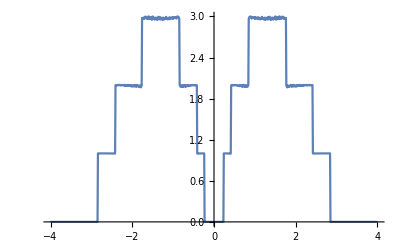
{1.30028,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
f2:=f2=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"]]
f3:=f3=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp7.csv"]]
 f4:=f4=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp7.csv"]]
 f5:=f5=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp7.csv"]]
 f6:=f6=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp7.csv"]]
 f7:=f7=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp7.csv"]]
 f8:=f8=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp7.csv"]]
 f9:=f9=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"]]
 f10:=f10=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"]]
 f11:=f11=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"]]
 f12:=f12=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/12imp/12imp7.csv"]]
```

```mathematica
k2:=k2=Table[{ω,f2[ω]},{ω,0,4,0.0005}]
k3:=k3=Table[{ω,f3[ω]},{ω,0,4,0.0005}]
k4:=k4=Table[{ω,f4[ω]},{ω,0,4,0.0005}]
k5:=k5=Table[{ω,f5[ω]},{ω,0,4,0.0005}]
k6:=k6=Table[{ω,f6[ω]},{ω,0,4,0.0005}]
k7:=k7=Table[{ω,f7[ω]},{ω,0,4,0.0005}]
k8:=k8=Table[{ω,f8[ω]},{ω,0,4,0.0005}]
k9:=k9=Table[{ω,f9[ω]},{ω,0,4,0.0005}]
k10:=k10=Table[{ω,f10[ω]},{ω,0,4,0.0005}]
k11:=k11=Table[{ω,f11[ω]},{ω,0,4,0.0005}]
```

```mathematica
f[ω_]:={{0,Pri[[ω*2000+1]][[2]]},{2,k2[[ω*2000+1]][[2]]},{3,k3[[ω*2000+1]][[2]]},{4,k4[[ω*2000+1]][[2]]},{5,k5[[ω*2000+1]][[2]]},{6,k6[[ω*2000+1]][[2]]},{7,k7[[ω*2000+1]][[2]]},{8,k8[[ω*2000+1]][[2]]},{9,k9[[ω*2000+1]][[2]]},{10,k10[[ω*2000+1]][[2]]},{11,k11[[ω*2000+1]][[2]]}}
```

```mathematica
φ[ω_]:=Interpolation[f[ω]]
```

```mathematica
sloap[ω_,n_]:=Abs[(φ[ω][n]-φ[ω][n+.001])/0.001]
```

```mathematica
s[ω_,l_]:=s[ω,l]=Table[sloap[ω,k],{k,Range[0,l,0.01]}]
```

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}], μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{1,1}}->ω+ⅈ*0.0001-0]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/12imp/12imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};{list[[Position[list,Min[list]][[1,1]],1]],Min[list],list}]
```

```mathematica
misfit1[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}], μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{1,1}}->ω+ⅈ*0.0001-0]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/12imp/12imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};{list[[Position[list,Min[list]][[1,1]],1]],Min[list],list}]
```

```mathematica
misfit2[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}], μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.0001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]];imp3=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]];imp5=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{1,1}}->ω+ⅈ*0.0001-0]]];imp7=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.0001-0]]];imp8=Inverse[Module[{gg=β[ω,0.0001,1,0]},ReplacePart[gg,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.0001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.0001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.0001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/12imp/12imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};{list[[Position[list,Min[list]][[1,1]],1]],Min[list],list}]
```

```mathematica
misfit1[0.3,1.5,0]
```

```mathematica
Table[υ[0.7,1.5,0.2],100]
```

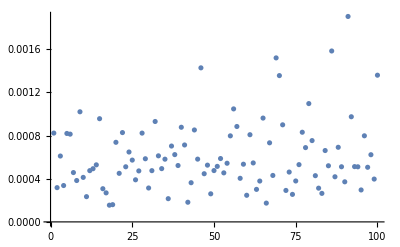

```mathematica
ListPlot[%94,PlotRange->All]
```

```mathematica
Table[υ[0.7,1.7,0.2],100]
```

```mathematica
κ27:=κ27=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells2imp/2imp7.csv"]
```

```mathematica
κ37:=κ37=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells3imp/3imp7.csv"]
```

```mathematica
κ47:=κ47=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells4imp/4imp7.csv"]
```

```mathematica
κ57:=κ57=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells5imp/5imp7.csv"]
```

```mathematica
κ67:=κ67=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells6imp/6imp7.csv"]
```

```mathematica
κ77:=κ77=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells7imp/7imp7.csv"]
```

```mathematica
κ87:=κ87=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells8imp/8imp7.csv"]
```

```mathematica
κ97:=κ97=Import["/home/shardulmukim/9imp7.csv"]
```

```mathematica
κ107:=κ107=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells10imp/10imp7.csv"]
```

```mathematica
κ117:=κ117=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells11imp/11imp7.csv"]
```

```mathematica
κ127:=κ127=Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells12imp/12imp7.csv"]
```

```mathematica
υ[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}], μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];
m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ27[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ37[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ47[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ57[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ67[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ77[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ87[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ97[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ107[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ117[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- κ127[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11,ρ12};(*Print[list];*)list(*list[[Position[list,Min[list]][[1,1]],1]],Min[list]*)(*,ListLinePlot[m5],
{μ3,μ4,μ5,μ6}*)(*,{μ1+μ3+μ5+μ8}*)]
```

```mathematica
Timing[υ[0.7,1.75,.0]]
```

{1.57131,{0.00162028,0.000977105,0.000746467,0.000849202,0.00108719,0.00151132,0.00205252,0.00284124,0.003067,0.00371978,0.00435192}}

```mathematica
ζ=Table[υ[0.7,1.75,0],2000]
```

{{0.0012455,0.00047964,0.000246635,0.000326699,0.00065273,0.00113941,0.00173078,0.00259888,0.0030221,0.00375609,0.00447223},{0.000733525,0.000198104,0.000139596,0.000383845,0.000836792,0.0014504,0.00214592,0.00315613,0.00363552,0.00445143,0.00524628},1997,{0.000375808,0.000266397,0.000580804,0.00114732,0.00189734,0.00275702,0.00368059,0.00492878,0.00546738,0.00643682,0.00735175}}
 |  |  |  |

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{15.5,GrayLevel[0]},PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Export["error4imp.csv",ζ]
```

error4imp.csv

```mathematica
Import["error4imp.csv"]
```

{{0.0012455,0.00047964,0.000246635,0.000326699,0.00065273,0.00113941,0.00173078,0.00259888,0.0030221,0.00375609,0.00447223},{0.000733525,0.000198104,0.000139596,0.000383845,0.000836792,0.0014504,0.00214592,0.00315613,0.00363552,0.00445143,0.00524628},1997,{0.000375808,0.000266397,0.000580804,0.00114732,0.00189734,0.00275702,0.00368059,0.00492878,0.00546738,0.00643682,0.00735175}}
 |  |  |  |

```mathematica
Show[%19,PlotLabel->None,LabelStyle->{GrayLevel[0],Italic}]
```

-Graphics-

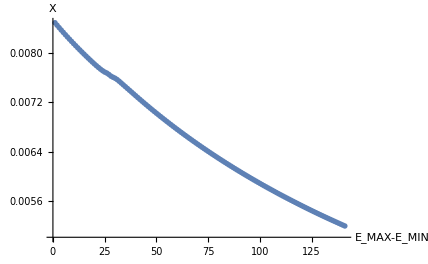
```mathematica
ξ=-Graphics-
```

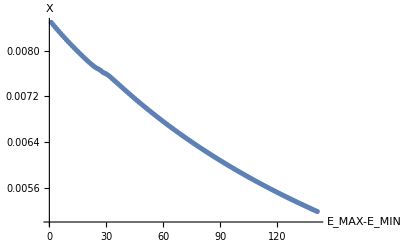

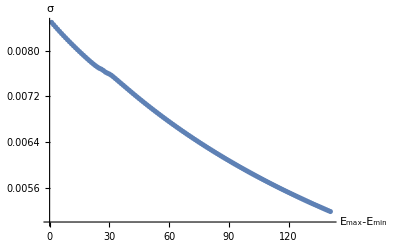

```mathematica
Show[ξ,AxesLabel->{HoldForm[HoldForm[Subscript[Ε, max]-Subscript[Ε, min]]],HoldForm[σ]},PlotLabel->None]
```

```mathematica
Show[%46,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
%46
```

-Graphics-

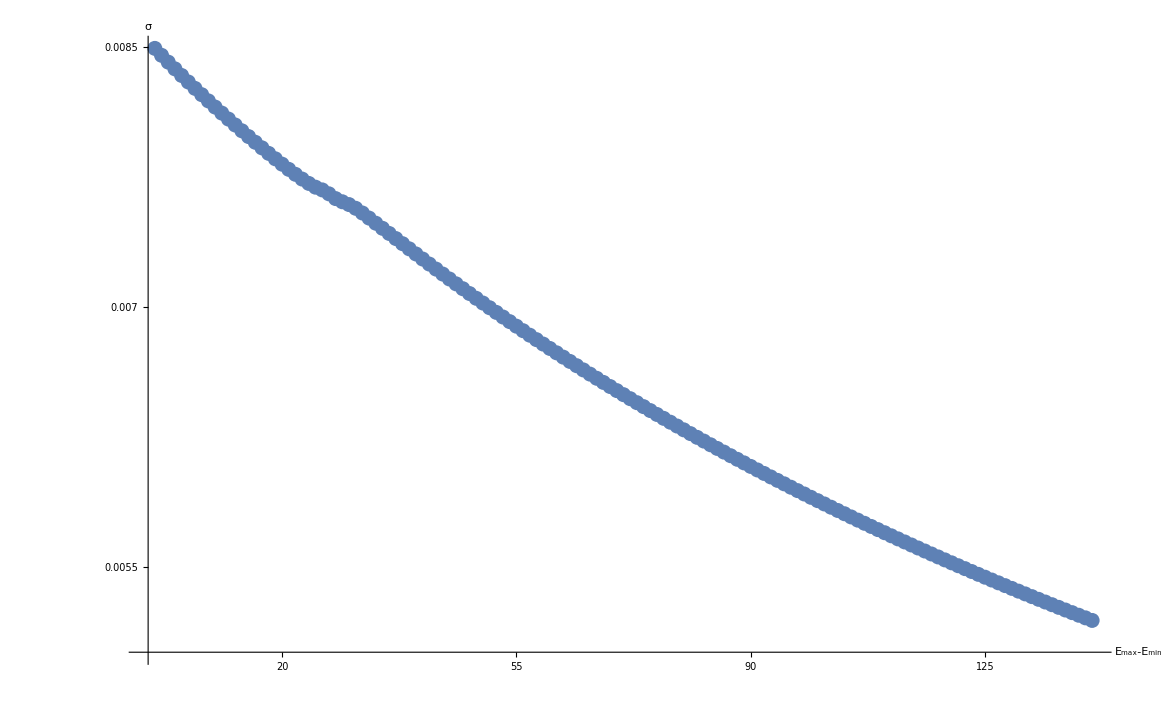

```mathematica
Show[%60,PlotLabel->None,LabelStyle->{40,GrayLevel[0]},Ticks->{Range[20,140,35],Range[0.0055,0.0085,0.0015]}]
```

```mathematica
DynamicModule[{ξ=Scaled[{0.5,0.5}]},ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Detailed",FrameLabel->{{HoldForm[χ[n]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{45.5,GrayLevel[0]},PlotRange->All,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1],Epilog->{Dynamic[Locator[Dynamic[ξ],Show[%162,Background->White,ImageSize->900]]]},ImageSize->2000]]
```

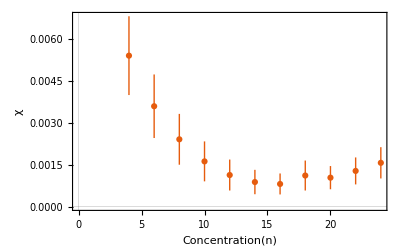

```mathematica
Show[%201,FrameLabel->{{HoldForm[χ],None},{HoldForm[Concentration[n]],None}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

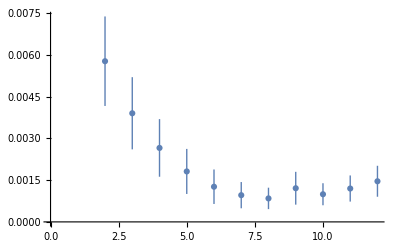

```mathematica
ListPlot[{{2,Around[Table[ζ[[x]][[1]],{x,1,2000}]]},{3,Around[Table[ζ[[x]][[2]],{x,1,2000}]]},{4,Around[Table[ζ[[x]][[3]],{x,1,2000}]]},{5,Around[Table[ζ[[x]][[4]],{x,1,2000}]]},{6,Around[Table[ζ[[x]][[5]],{x,1,2000}]]},{7,Around[Table[ζ[[x]][[6]],{x,1,2000}]]},{8,Around[Table[ζ[[x]][[7]],{x,1,2000}]]},{9,Around[Table[ζ[[x]][[8]],{x,1,2000}]]},{10,Around[Table[ζ[[x]][[9]],{x,1,2000}]]},{11,Around[Table[ζ[[x]][[10]],{x,1,2000}]]},{12,Around[Table[ζ[[x]][[11]],{x,1,2000}]]}}]
```

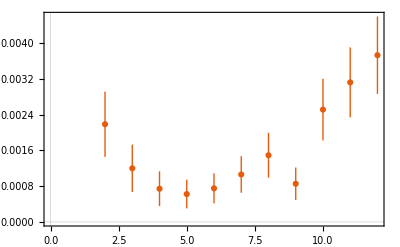

```mathematica
ListPlot[{{2,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{3,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{4,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{5,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{7,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{9,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{11,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Scientific"]
```

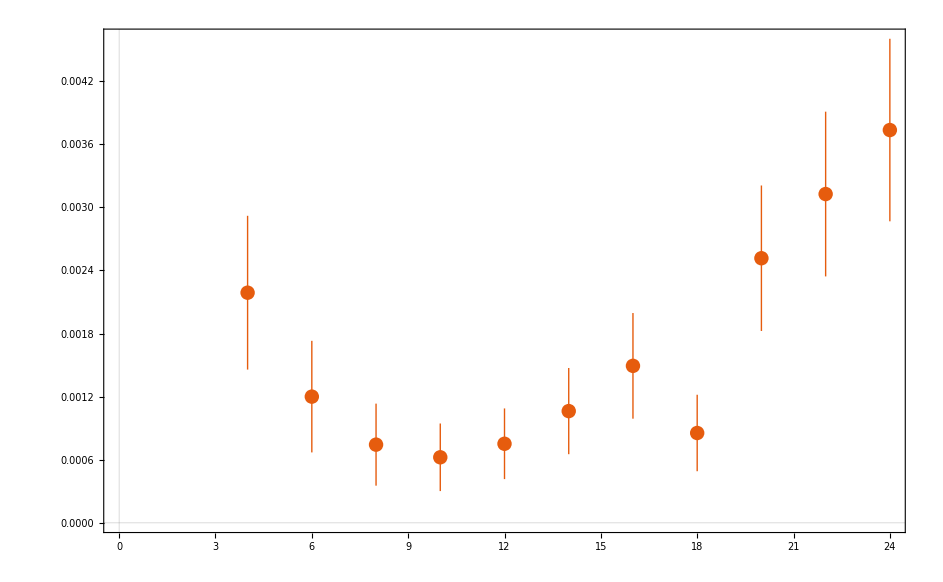

```mathematica
ListPlot[{{4,Around[Table[ζ⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[ζ⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[ζ⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[ζ⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[ζ⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[ζ⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[ζ⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[ζ⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[ζ⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[ζ⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[ζ⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Scientific"]
```

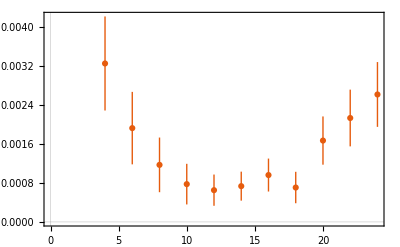

```mathematica
ListPlot[{{4,Around[Table[%189⟦x⟧⟦1⟧,{x,1,2000}]]},{6,Around[Table[%189⟦x⟧⟦2⟧,{x,1,2000}]]},{8,Around[Table[%189⟦x⟧⟦3⟧,{x,1,2000}]]},{10,Around[Table[%189⟦x⟧⟦4⟧,{x,1,2000}]]},{12,Around[Table[%189⟦x⟧⟦5⟧,{x,1,2000}]]},{14,Around[Table[%189⟦x⟧⟦6⟧,{x,1,2000}]]},{16,Around[Table[%189⟦x⟧⟦7⟧,{x,1,2000}]]},{18,Around[Table[%189⟦x⟧⟦8⟧,{x,1,2000}]]},{20,Around[Table[%189⟦x⟧⟦9⟧,{x,1,2000}]]},{22,Around[Table[%189⟦x⟧⟦10⟧,{x,1,2000}]]},{24,Around[Table[%189⟦x⟧⟦11⟧,{x,1,2000}]]}},PlotTheme->"Scientific"]
```

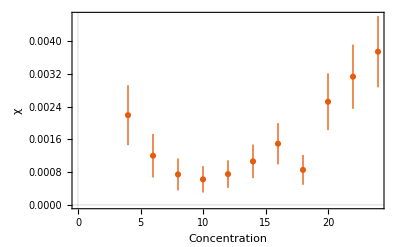

```mathematica
Show[%186,FrameLabel->{{HoldForm[χ],None},{HoldForm[Concentration],None}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

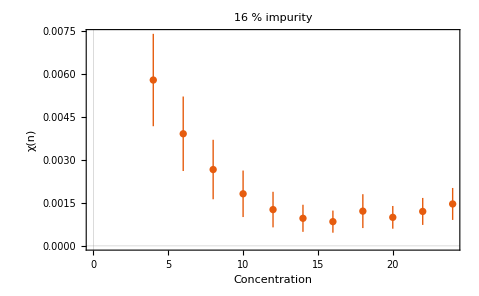

```mathematica
Show[%179,FrameLabel->{{HoldForm[χ[n]],None},{HoldForm[Concentration],None}},PlotLabel->HoldForm[16 % impurity],LabelStyle->{GrayLevel[0]}]
```

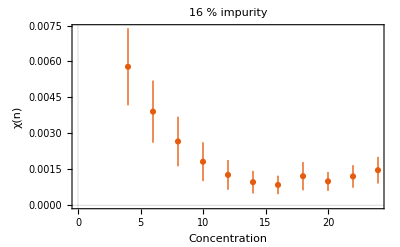

```mathematica
Show[%180,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],Method->{"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

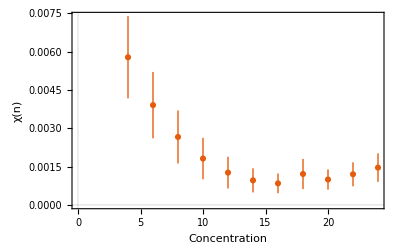

```mathematica
Show[%181,PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

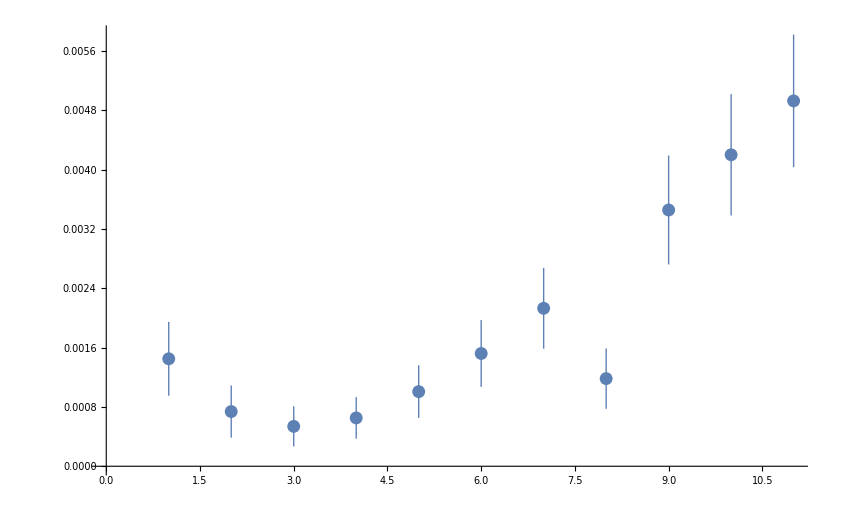

```mathematica
ListPlot[{Around[Table[%161[[x]][[1]],{x,1,2000}]],Around[Table[%161[[x]][[2]],{x,1,2000}]],Around[Table[%161[[x]][[3]],{x,1,2000}]],Around[Table[%161[[x]][[4]],{x,1,2000}]],Around[Table[%161[[x]][[5]],{x,1,2000}]],Around[Table[%161[[x]][[6]],{x,1,2000}]],Around[Table[%161[[x]][[7]],{x,1,2000}]],Around[Table[%161[[x]][[8]],{x,1,2000}]],Around[Table[%161[[x]][[9]],{x,1,2000}]],Around[Table[%161[[x]][[10]],{x,1,2000}]],Around[Table[%161[[x]][[11]],{x,1,2000}]],Around[Table[%161[[x]][[12]],{x,1,2000}]]}]
```

```mathematica
Table[υ[0.7,1.5,0],10]
```